```mathematica
ser=Series[f[x,y],{x,0,2},{y,0,2}]
```

(f[0,0]+f^(0,1)[0,0] y+1/2 f^(0,2)[0,0] y^2+O[y]^3)+(f^(1,0)[0,0]+f^(1,1)[0,0] y+1/2 f^(1,2)[0,0] y^2+O[y]^3) x+(1/2 f^(2,0)[0,0]+1/2 f^(2,1)[0,0] y+1/4 f^(2,2)[0,0] y^2+O[y]^3) x^2+O[x]^3

```mathematica
Collect[ser,{x,y}]
```

f[0,0]+y f^(0,1)[0,0]+1/2 y^2 f^(0,2)[0,0]+x (f^(1,0)[0,0]+y f^(1,1)[0,0]+1/2 y^2 f^(1,2)[0,0])+x^2 (1/2 f^(2,0)[0,0]+1/2 y f^(2,1)[0,0]+1/4 y^2 f^(2,2)[0,0])

```mathematica
u
```

```mathematica
(0.0528-0.0438)/0.0438
```

0.205479

```mathematica
(0.0438-0.0447)/0.0447
```

-0.0201342

```mathematica
(0.0316-0.0447)/0.0316
```

-0.414557

```mathematica
(0.0261-0.0316)/0.0316
```

-0.174051

```mathematica
(0.874-0.865)/0.865
```

0.0104046

```mathematica
1.274-1.381
```

```mathematica
mytot[x_]:=Total[IntegerDigits[Prime[x],2,1000]]
mylist=Table[mytot[x],{x,1,100}]
```

{1,2,2,3,3,3,2,3,4,4,5,3,3,4,5,4,5,5,3,4,3,5,4,4,3,4,5,5,5,4,7,3,3,4,4,5,5,4,5,5,5,5,7,3,4,5,5,7,5,5,5,7,5,7,2,4,4,5,4,4,5,4,5,6,5,6,5,4,6,6,4,6,7,6,7,8,4,5,4,5,5,5,7,5,7,7,4,5,6,7,6,8,7,7,7,8,8,3,4,5}

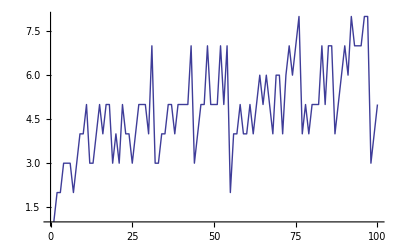

```mathematica
ListPlot[mylist,Joined->True]
```

```mathematica
mytot[x_]:=IntegerDigits[Prime[x],2,100]
mylist=Table[mytot[x],{x,1,10000}];
ArrayPlot[mylist]
```

-Graphics-